# Report Project 1

Course code: IX1500 - Discrete Mathematics
Date: 2017-10-04

Evan Saboo, saboo@kth.se
Xing Guan, xguan@kth.se

Task 1a: RSA cipher

## Summary

### Task

Professor Alice is sending a problem to the student Bob. We are supposed to solve Bob’s problem by cracking the cipher first which is sent by Alice to Bob.

### Result

By using Bobs public key (n_Bob,e_Bob) and Alice public key (n_Alice,e_Alice), we were able to decrypt the cipher message sent from Alice to Bob:

Congratulations! You have now managed to crack the RSA cipher. Your task is as follows: write a method RSAcrack[cipher,n,e] that will crack a standard RSA cipher and delivers clear text from the string cipher. When you are finished with your method, you should investigate how long it will take to crack the cipher of the Swedish text DISKRET MATTE, DE E FETT NAIS! for different sizes on your public key n (100-200 bits). Visualize your results in a proper graph. It is very important that you study the section 2.3 in the instructions. Your graph should lead you to a model where you can predict how long it would take to crack a cipher if n is 1024, 2048 bits or 4096 bits with your computer.

## Cracking the cipher

By using the census method we can estimate the exact probability of each rank in a poker game.
   (|a|)/(|h|)= probability of a in h

 |a| is the amount of possibilites you can get on the total amount |h| 
 

First we construct the 5 cards 8,9,10,J,Q,K,A with their respective colors. Every card has 4 distinct colors (Red,  Black, Green, Blue), which means that we have to separate them by distinct numbers. This is the the result we get for one deck:

{{108,109,110,111,112,113,114},
{208,209,210,211,212,213,214},
{308,309,310,311,312,313,314},
{408,409,410,411,412,413,414}}

We represent the hundreds digit as the color and the two last sub values as the cards value, e.g. the card 108 has the color Red and has the card value 8 while the card 208 has the same card value but not the same color.

We construct another identical deck and join it with the first deck to get a every value we need from the two deck in one set:

{108,108,109,109,110,110,111,111,112,112,113,113,114,114,
208,208,209,209,210,210,211,211,212,212,213,213,214,214,
308,308,309,309,310,310,311,311,312,312,313,313,314,314,
408,408,409,409,410,410,411,411,412,412,413,413,414,414}

We also sorted the set above in numerical order to calculate the probability for each rank without adding extra condition to each calculation.

The last step is to generate all possible hands with five card in each hand:

{{108,108,109,109,110},
{108,108,109,109,110},
«3819813»,
{412,413,413,414,414}}
   
 The total possible hands we can get is 3 819 816.

### One pair

To calculate the probability for getting lowest rank one pair, we constructed a function called pairQ to sum up all generated hands which contains one pair. We excluded all the colors from every card to check if the two cards are identical.
We also excluded all the hands which contains; two pairs, three of a kind and flush, because we want to filter out every rank higher than one pair. There are even higher ranked poker hands which we want to filter out but we don’t need to because our filtered ranks already covers the higher ranks, e.g. one of a kind filters also four and five of a kind. The same principle is used when calculating the probability of almost every rank.   

The total amount of hands which only contains one pair is 2 002 560. 
By dividing the total number of hands containing one pair with the total possible hands we get the exact probability of one pair:

11920/22737≈ 52.426%

### Two pairs

The second lowest poker rank is two pair. We defined another function for two pairs and checked every possible hand by filtering out all hands which contains two pairs and doesn’t contain higher rank than our current rank.

The total amount of hands which only contains two pairs is 438 480. 
The total number of possibilities of two pairs divided by the total number of hands is the probability of the current rank:

1305/7579≈ 17.219%

### Three of a kind

We applied the same idea as in our two previous calculations when calculating the probability of getting three of a kind. Our new function threeKindQ filtered out four of a kind and full hand.

The total amount of hands which only contains three of a kind is 376 320 and the probability of the rank is:

2240/22737≈ 9.852%

### Four of a kind

To get the total amount of possible hands which contains four of a kind, we need to only filter out five of a kind.
The total amount of hands which only contains four of a kind is 23 520, and the probability of the rank is:

140/22737≈ 0.616%

### Five of a kind

Five of a kind contains 5 identical cards which doesn’t necessary need to have the same color. the rank is distinct to every other rank which makes it easier for us to get an answer because we don’t need to exclude any other rank.

The total amount of hands that contains only five of a kind is 392, and the probability of getting the rank is:

 7/68211≈ 0.01%

### Full hand

Full hand is the combination of 3 identical values followed by 2 different identical values, without taking colors into account. All ranks higher than full hand does not overlap the rank and we don’t need to filter anything out of our calculation.

By using the function fullHand, we get 65 856 amount of hand that contains the rank , and we get the probability:

 392/22737≈ 1.724%

### Straight

The rank straight is a bit different from previous ranks. We have to check if very hand has an ascending order where the first card is x and the second is x+1, the third is x+2, the fourth is x+3 and the last is x+4. By sorting every hand we can safely assume the lowest card value is always placed to the left of the hand and the highest to the right:
x_1 ≤ x_2 ≤ x_3 ≤ x_4 ≤ x_5 

flush[h]=h-h[[1]]=={0,1,2,3,4}

The function above takes the most left card and substitutes it with every card in the hand to check if it’s in ascending order from right to left.

The only thing we have to filter out of from our calculation is the highest rank straight flush. 
We can substitute the total all hands containing straight flush from our total amount of straight hands because every hand containing straight flush also contains the rank straight.
 
The answer we got is 98 304 amount of hands that contains straight and the probability of the rank is:

1360/53053≈ 2.563%

### Flush

The function “flush” is defined to a point where every card in a deck has to have the same color to be included in our total amount. We check if every cards hundred number is the same as the rest by dividing with 100. We also excluded every hand which contain the highest rank “straight flush” by substitution. 

The final answer we got is 8 008 possible hands which contains flush as the highest rank.
The probability of getting flush is:

953/477477≈ 0.2%

### Straight flush

To find every hand that contains straight flush we need to check if every all cards in each hand is in ascending order from left to right and we need to check if they all have the same color.
The function defined below checks if every card in the hand follows the ascending order from 0 to 4 by substituting every card by the first card, e.g. every card in the hand {108, 109, 110, 111, 112} gets substituted by 108 {(108 - 108), (109 - 108), (110 - 108), (111 - 108), (112- 108)}.
At the same time we are checking if the color is the same by not filtering the hundred number from every card.

straightFlush[h]=h-h[[1]]=={0,1,2,3,4}


 384 is the total amount of straight flush we got from all possible hands and the probability of it is:

16/159159≈ 0.1%

### Nothing

Calculating the probability nothing is pretty easy, we just have to exclude all hands which contains any kind of rank and count all hands with no rank.
We know that one pair filters out two pair, three, four, five of a kind and full hand, which is why only need one condition for the
 ranks. We also have to exclude flush and straight but not straight flush because it’s already filtered out.

 685 440 is total amount of hands with no rank and the probability of getting nothing is:

8160/53053≈ 15.381%

## Code

```mathematica
ClearAll["`*"]
```

```mathematica
nAlice=14625052655936968690439555839903578410656653152402266773966305647313;
eAlice=9103;
```

```mathematica
nBob=891257371165353198597686733461449215081540410212576138836198818353;
eBob=6389;
```

```mathematica
cipher={4430210573981968733755487447818174029880701596884938356564639003222,2851153559114750987221731555966122250132614620940651980091426872783,7706806242317911603638504323916964668918097951180075641184510131492,3684227409638269668959612918228029487936911649602484180495870360134,118390233898339944208891887229177617429671446231727377499079969939,11722755771961643408261179942790037153532726213028762901063706465880,13859812858423457720552211210177480158021647193707898449643563546715,8458200553283608142592103589289032864817455387331640007234518389001,4203062251335458332458951560795586742826858693125368654700629553235,11246017592897572378455633552556960091533916541949272900160606355164,528729157482321024630053104368111400799635858352035984875544277541,14149609332514930578966644135292557372570883055216115495760639164502,6806693065526086081574819023329054541636484663342321332752294055806,10173212145631688548727430811241580523813551542356631310237779750220,6759760040422316973322423168431166905944837651248859901210533615722,11488644301666039406597033276777701689096765993957684011886918061630,10421162414768710251337302689028405059375889881305351342596162625647,9496359638348947223087997149242581766202717301485526573539185466328,6021527813042783330194131859432644092333420618174656828129608651886,1862712526928231860818857411345402991522792361353775067366437910859,5770870235309404532139302393417410250573907045700501009827409811147,7754796273877044686482387739917927617087893337176831108280229804774,1689445149306311402232833597026076887079752228378923964144759423086,1448530945006829418385610770415140752515002298435493622427431846992,7445869507503892181715468267483205548161014207123217105479157092169,10975830923316626122520530596740793665823967057824410678091427215458,9807539864876132360289770201821020858873102738795986884424480971219};
```

The numbers is the list seems to be of the same size. Why?

Motivate your selected mathematical model!

```mathematica
{t1,f1}=AbsoluteTiming[FactorInteger[nBob]]
```

{853.397,{{457792861431456494922119050690577,1},{1946857293446017662241143108141089,1}}}

```mathematica
{{pBob,p},{qBob,q}} = f1
```

{{457792861431456494922119050690577,1},{1946857293446017662241143108141089,1}}

```mathematica
ϕBob=(pBob-1)(qBob-1)
```

891257371165353198597686733461446810431385532738418975574039986688

```mathematica
dBob=PowerMod[eBob,-1,ϕBob]
```

67796381653836540071760174121499945197942302224271657869617065821

```mathematica
For[i = 1, i < Length[cipher] +1, i++, 
cipher[[i]] = PowerMod[cipher[[i]],eAlice,nAlice]

]
```

```mathematica
For[i = 1, i < Length[cipher] +1, i++, 
cipher[[i]] = PowerMod[cipher[[i]], dBob, nBob]

]
```

```mathematica
crackedMsg = cipher;
```

```mathematica
B= 256;
```

```mathematica
For[i = 1, i < Length[cipher]+1, i++, 
q=cipher[[i]];ascii={};
While[q≠0,
AppendTo[ascii,Mod[q,B]];
q=Quotient[q,B]
];
crackedMsg[[i]] =FromCharacterCode[ascii];
Print[crackedMsg[[i]]]
]
```

Congratulations! You have

now managed to crack the R

SA cipher. Your task is as

follows: write a method R

SAcrack[cipher,n,e] that w

ill crack a standard RSA c

ipher and delivers clear t

ext from the string cipher

. When you are finished wi

th your method, you should

investigate how long it w

ill take to crack the ciph

er of the Swedish text DIS

KRET MATTE, DE E FETT NAIS

! for different sizes on y

our public key n (100-200

bits). Visualize your resu

lts in a proper graph. It

is very important that you

study the section 2.3 in

the instructions. Your gra

ph should lead you to a mo

del where you can predict

how long it would take to

crack a cipher if n is 102

4, 2048 bits or 4096 bits

with your computer.

```mathematica
StringJoin[crackedMsg]
```

Congratulations! You have now managed to crack the RSA cipher. Your task is as follows: write a method RSAcrack[cipher,n,e] that will crack a standard RSA cipher and delivers clear text from the string cipher. When you are finished with your method, you should investigate how long it will take to crack the cipher of the Swedish text DISKRET MATTE, DE E FETT NAIS! for different sizes on your public key n (100-200 bits). Visualize your results in a proper graph. It is very important that you study the section 2.3 in the instructions. Your graph should lead you to a model where you can predict how long it would take to crack a cipher if n is 1024, 2048 bits or 4096 bits with your computer.

Task 1b: Prediction and selection of mathematical model

## Summary

### Task

Write a method RSAcrack[cipher,n,e] that will crack a standard RSA cipher and delivers clear text from the string cipher. Also using the function and other functions we gonna investigate how long it will take to crack the cipher of the Swedish text DISKRET MATTE, DE E FETT NAIS! for different sizes on our public key n (100-200 bits). Visualize the results in a proper graph. The created graph should predict how long it would take to crack a cipher if n is 1024, 2048 bits or 4096 bits with our computer.

### Result

Using the formula m_Alice≡_n_Bob c_Alice^d_Bob and given c_Alice and n_Bob we could calculate decryption key, d_Bob which is implemented in the method RSAcrack[cipher, n, e]. For more detail, see the explanation under subsection “RSAcrack method”.

The exponential function is used to our model. Using the graph which was created, we could find our mathematical model to calculate the time it takes to crack the cipher if  n is 1024, 2048 bits or 4096 bits with our computer. The answer is presented in the table below.

Size,bit | Time,year
1024 | 7.271*10^23
2048 | 4.076*10^60
4096 | 1.282*10^134

## The selected model and size of the cipher

### RSAcrack method

RSAcrack method use the formula m_Alice≡_n_Bob c_Alice^d_Bob to crack the cipher. Given the  c_Alice and n_Bob we need to find out d_Bob.

In order to do find d_Bob we use the Mathematica function, FactorInteger[n] to break down the n to two primes where n is the multiplication of two large primes and is public number from the person where the message is sent to. In this case it is Bob the message is sending to.

Let the two primes defined as P and Q where P ≠ Q. We can now calculate phi, ϕ=(p-1)(q-1) which is used to calculate the decryption key, d. Decryption key is calculated using the help of the formula d e≡_ϕ 1. Where e is known due to it is a public number and we can use the inverse of e  and mod the result of it with ϕ which in turn give us d. 

With  c_Alice, n_Bob and d_Bobwe can now calculate the m_Alice. To begin with we get the ASCII message with 256 in base and let us call it "Pre m_Alice". That means we need to convert the "Pre m_Alice" to ASCII using the predefined method Quotient from Mathematica. Having the ASCII representative text we use FromCharacterCode[ASCII numbers] to get the letter and later join on all the letters to a text.

### The selected model

We tried different function where the exponential function makes all the data dots act as a straight line. We can then draw the conclusion that if the data fits a straight line then that is the function we are using.

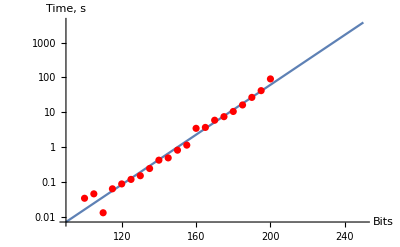

Our data contains n bits as parameter x which need to be cracked and time as parameter y. Knowing the data and exponential function we need to make the time, y logarithmic. After having treated time to logarithmic one we used the predefined function solution  = FindFit[data, a*sizeOfn+b,{a,b}, x] to find out parameter a and b. A and b is used to create our function y[sizeOfn]=ⅇ^(a *sizeOfn+b)/.solution.

We have now our model which is y[sizeOfn]=ⅇ^(a *sizeOfn+b)/.solution, where a is 0.0826339 and b equals to -12.4073. The results is then calculated by put the parameter 1024, 2048 and 4096 into the function. Which gives 7.271*10^23, 4.076*10^60 and  1.282*10^134 years respectively. The result was first in seconds and by dividing it with 60*60*24*365 which gives us the number of years it takes.

Size,bit | Time,year
1024 | 7.271*10^23
2048 | 4.076*10^60
4096 | 1.282*10^134

## Code

```mathematica
message = "DISKRET MATTE, DE E FETT NAIS!";
```

```mathematica
(* Make sure a long text break down to the size that is smaller than n *)
splitText[message_, a_, b_]:= Module[{Bytes, ascii, F, B, i, eachLineBits, case},
eachLineBits = a +b;         (* the maximum size of each line *)
Bytes = Floor[eachLineBits/8];
case = Bytes*8;
B = Which[case == eachLineBits, Bytes-1, True, Bytes];  
ascii={};
For[i=1, i <StringLength[message]/B+1, i++, 
F =Which[i*B > StringLength[message], StringLength[message], True, i*B];
AppendTo[ascii, StringTake[message,{(i-1)*B +1, F}]]
]; 
ascii
]
```

```mathematica
(* Generate the cipher with different size of n,(a+b) *)
genCipher[message_, a_, b_] := 
Module[{ pPerson, qPerson, ϕPerson,ePerson, m, nPerson, c, i, rnd, ascii},
pPerson = NextPrime[RandomInteger[{2^a, 2^a}]];
qPerson = NextPrime[RandomInteger[{2^b, 2^b}]];
ϕPerson=(pPerson-1)(qPerson-1);
nPerson = pPerson*qPerson;
rnd:=RandomInteger[{10^3,10^4}];
While[GCD[ePerson=rnd,ϕPerson]≠1];
c = splitText[message, a, b];
For [i = 1, i < Length[c]+1, i++, 
c[[i]] = ToCharacterCode[c[[i]] ]. 256^(Range[StringLength[c[[i]]]]-1);
c[[i]] = PowerMod[c[[i]] , ePerson, nPerson];
];
{nPerson, ePerson,c}       (* return n and e numbers, c is the cipher *)
]
```

```mathematica
(*Task 2*) (* function that crack the cipher to clear text *)
RSAcrack[cipher_, n_, e_] := 
Module[{t, f, pPerson, qPerson, ϕPerson, dPerson, mFromPerson, mInAscii, B, clearText, i, q, ascii,c},
{t, _G}=AbsoluteTiming[
{{pPerson,_V},{qPerson,_L}} = FactorInteger[n];
ϕPerson=(pPerson-1)(qPerson-1);
dPerson=PowerMod[e,-1,ϕPerson];
c =cipher;
For[i = 1, i <Length[cipher]+1, i++,
mFromPerson = PowerMod[cipher[[i]],dPerson,n];
q=mFromPerson;ascii={};
While[q≠0,
AppendTo[ascii,Mod[q,256]];       
q=Quotient[q,256]
];
c[[i]] = FromCharacterCode[ascii];
];
];
clearText = StringJoin[c];
{t, clearText}     (* Return the time and clearText *)
]
```

```mathematica
(* This function repeatly create the cipher with different size and crack it *)
genData[message_, amountData_, startBit1_, startBit2_] := Module[{n, e, c, data, t, s1, s2, i, sList, tList, sTotal},
data = {};
sList = {};
tList = {};
(* each iteration increases the n with 5 bits, starting 100 and end at 200 bits *)
For[i=0, i < amountData+1, i++,  
s1=startBit1 + i*2 ;
s2 = startBit2 +i*3;
sTotal = s1 + s2;
{n,e,c} = genCipher[message, s1 , s2 ];
{t, _m} = RSAcrack[c,n,e];
temp = {(s1+s2), t};
AppendTo[data,temp];
AppendTo[sList, sTotal];
AppendTo[tList, t];
];
{data, sList, tList}     (* It gives the data(bits, x and time, y), sList(bits), tList(time) *)
]
```

```mathematica
{data, sList, tList} = genData[message, 20, 49,51]        (* generate the data to make our model *)
```

{{{100,0.0334767},{105,0.0448425},{110,0.0128079},{115,0.0626706},{120,0.0865574},{125,0.116783},{130,0.148939},{135,0.24041},{140,0.417705},{145,0.485974},{150,0.809954},{155,1.13113},{160,3.44232},{165,3.65593},{170,5.88853},{175,7.45143},{180,10.5222},{185,16.1843},{190,26.7199},{195,41.7943},{200,90.8674}},{100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200},{0.0334767,0.0448425,0.0128079,0.0626706,0.0865574,0.116783,0.148939,0.24041,0.417705,0.485974,0.809954,1.13113,3.44232,3.65593,5.88853,7.45143,10.5222,16.1843,26.7199,41.7943,90.8674}}

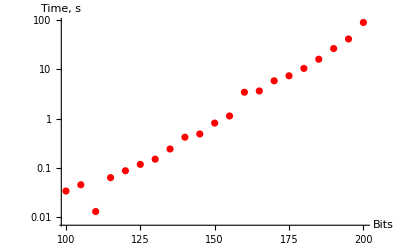

```mathematica
dataPlot = ListLogPlot[data, AxesLabel -> {"Bits", "Time, s"}, PlotStyle-> Red]
```

```mathematica
data2=Transpose[{sList,Log[tList]}];
```

```mathematica
solution=FindFit[data2,a x+b,{a,b},x](* to find out parameter a and b *)
```

{a→0.0826339,b→-12.4073}

```mathematica
y[x_]=ⅇ^(a x+b)/.solution (* this is our model *)
```

ⅇ^(-12.4073+0.0826339 x)

```mathematica
modelplot = LogPlot[y[x], {x,90,250}, AxesLabel -> {"Bits", "Time, s"}];
Show[modelplot, dataPlot]
```

-Graphics-

```mathematica
secToYear = 60*60*24*365;  (* seconds in a year *)
```

```mathematica
y[1024]/secToYear
```

7.26977×10^23

```mathematica
y[2048]/secToYear
```

4.07627×10^60

```mathematica
y[4096]/ secToYear
```

1.28158×10^134